# QED calculation: Peskin Sec. 5

## e^-e^+→γ γ : Peskin P.153-54

-Graphics-

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.4 (7 Jun 2016)

by Thomas Hahn

### Create Topology & Insert Particles

loading generic model file /Users/misho/.ghq/github.com/misho104/FeynLecture/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/misho104/FeynLecture/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counter terms of order 1

> 6 counter terms of order 2

classes model {SM} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 2 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

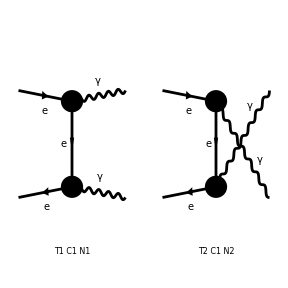

```mathematica
topologies=CreateTopologies[0,2->2];
diagrams=InsertFields[topologies,{F[2,{1}],-F[2,{1}]}->{V[1],V[1]},InsertionLevel->{Classes}];
Paint[diagrams];
```

### Pass the diagram to FormCalc

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA]
amplitude//.Abbr[]//.Subexpr[]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

in total: 2 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{V[1],k[3],0,{}},{V[1],k[4],0,{}}}][Alfa Pair2 π (4 Den[T,ME2]-4 Den[U,ME2]) Mat[F2]-4 Alfa π (Den[T,ME2]+Den[U,ME2]) Mat[F4]-Alfa π (8 Pair3 Den[T,ME2]-8 Pair4 Den[U,ME2]) Mat[F5]-Alfa Pair1 π (4 Den[T,ME2]-4 Den[U,ME2]) Mat[F6]]

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{V[1],k[3],0,{}},{V[1],k[4],0,{}}}][-4 Alfa π (Den[T,ME2]+Den[U,ME2]) Mat[<v1|-1,ec[3],ec[4],k[3]|u2>]-Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Mat[<v1|1,k[3]|u2>] Pair[ec[3],ec[4]]-Alfa π Mat[<v1|1,ec[4]|u2>] (8 Den[T,ME2] Pair[ec[3],k[1]]-8 Den[U,ME2] Pair[ec[3],k[2]])+Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Mat[<v1|1,ec[3]|u2>] Pair[ec[4],k[3]]]

Take an average for initial fermions

```mathematica
_Hel=0;
SquaredHelicityME=SquaredME[amplitude]//.HelicityME[amplitude]
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

1/2 Abb4 Alfa2 Pair2 π^2 Pair1^* (4 Den[T,ME2]-4 Den[U,ME2])^2+1/2 Alfa2 Pair1 π^2 (ME2-T) (ME2-U) Pair1^* (4 Den[T,ME2]-4 Den[U,ME2])^2+1/2 Abb14 Alfa2 Pair1 π^2 Pair2^* (4 Den[T,ME2]-4 Den[U,ME2])^2+1/2 Alfa2 (Abb1+2 ME2) Pair2 π^2 Pair2^* (4 Den[T,ME2]-4 Den[U,ME2])^2-2 Abb5 Alfa2 Pair1 Pair13 π^2 (4 Den[T,ME2]-4 Den[U,ME2]) (Den[T,ME2]+Den[U,ME2])+2 Abb7 Alfa2 Pair2 π^2 (4 Den[T,ME2]-4 Den[U,ME2]) (Den[T,ME2]+Den[U,ME2])-2 Abb8 Alfa2 Pair2 π^2 Pair1^* (4 Den[T,ME2]-4 Den[U,ME2]) (Den[T,ME2]+Den[U,ME2])+2 Abb10 Alfa2 π^2 Pair2^* (4 Den[T,ME2]-4 Den[U,ME2]) (Den[T,ME2]+Den[U,ME2])+8 Alfa2 (-Abb15-2 ME2 Pair13 Pair2) π^2 (Den[T,ME2]+Den[U,ME2])^2+1/2 Alfa2 (-Abb19-2 ME2 Pair2) π^2 Pair1^* (4 Den[T,ME2]-4 Den[U,ME2]) (8 Pair3 Den[T,ME2]-8 Pair4 Den[U,ME2])-1/2 Alfa2 (-Abb17-2 ME2 Pair12) π^2 Pair2^* (4 Den[T,ME2]-4 Den[U,ME2]) (8 Pair3 Den[T,ME2]-8 Pair4 Den[U,ME2])+2 Abb21 Alfa2 π^2 (Den[T,ME2]+Den[U,ME2]) (8 Pair3 Den[T,ME2]-8 Pair4 Den[U,ME2])+1/2 Alfa2 Pair1 (-Abb22-2 ME2 Pair13) π^2 (4 Den[T,ME2]-4 Den[U,ME2]) (8 Pair3^* Den[T,ME2]-8 Pair4^* Den[U,ME2])-1/2 Alfa2 Pair2 (-Abb3-2 ME2 Pair9) π^2 (4 Den[T,ME2]-4 Den[U,ME2]) (8 Pair3^* Den[T,ME2]-8 Pair4^* Den[U,ME2])+2 Abb12 Alfa2 π^2 (Den[T,ME2]+Den[U,ME2]) (8 Pair3^* Den[T,ME2]-8 Pair4^* Den[U,ME2])+1/2 Alfa2 (Abb18+2 ME2) π^2 (8 Pair3 Den[T,ME2]-8 Pair4 Den[U,ME2]) (8 Pair3^* Den[T,ME2]-8 Pair4^* Den[U,ME2])

What are these abbreviations?

```mathematica
Abbr[]
Subexpr[]
```

{F1→<v1|1|u2>,F2→<v1|1,ec[3]|u2>,F5→<v1|1,ec[4]|u2>,F6→<v1|1,k[3]|u2>,F3→<v1|-1,ec[3],ec[4]|u2>,F4→<v1|-1,ec[3],ec[4],k[3]|u2>,Pair12→Pair[e[3],ec[4]],Pair6→Pair[e[3],k[1]],Pair5→Pair[e[3],k[2]],Pair9→Pair[e[4],ec[3]],Pair8→Pair[e[4],k[1]],Pair7→Pair[e[4],k[2]],Pair13→Pair[e[4],k[3]],Pair1→Pair[ec[3],ec[4]],Pair3→Pair[ec[3],k[1]],Pair4→Pair[ec[3],k[2]],Pair10→Pair[ec[4],k[1]],Pair11→Pair[ec[4],k[2]],Pair2→Pair[ec[4],k[3]],Abb21→-Abb20+Abb6 Pair12,Abb10→Abb9+Abb8 Pair12,Abb16→Pair10 Pair5+Pair11 Pair6,Abb2→Pair3 Pair7+Pair4 Pair8,Abb7→Abb6+Abb5 Pair9,Abb12→-Abb11+Abb9 Pair9,Abb1→-2 ME2+2 Pair3 Pair5+2 Pair4 Pair6+S,Abb18→-2 ME2+2 Pair10 Pair7+2 Pair11 Pair8+S,Abb17→-2 Abb16+Pair12 (-2 ME2+S),Abb3→-2 Abb2+Pair9 (-2 ME2+S),Abb15→-Abb13+Abb14 Pair2 Pair9+Pair12 (Abb4 Pair13+Pair9 (ME2-T) (ME2-U)),Abb11→Pair4 (-ME2-2 Pair10 Pair13+T)+Pair3 (ME2+2 Pair11 Pair13-U),Abb20→Pair5 (-ME2-2 Pair2 Pair8+T)+Pair6 (ME2+2 Pair2 Pair7-U),Abb13→Pair13 (Pair2 (4 ME2-2 Pair3 Pair5-2 Pair4 Pair6-S-2 T)+Pair10 (T-U))+(ME2-T) (ME2-U)+Pair2 Pair8 (T-U),Abb9→Pair11 (ME2-T)+Pair10 (-ME2+U),Abb8→Pair4 (ME2-T)+Pair3 (-ME2+U),Abb4→Pair4 (-ME2+T)+Pair3 (-ME2+U),Abb5→Pair5 (ME2-T)+Pair6 (-ME2+U),Abb14→Pair5 (-ME2+T)+Pair6 (-ME2+U),Abb6→Pair7 (ME2-T)+Pair8 (-ME2+U),Abb19→-Pair2 (ME2+U)+Pair10 (-T+U),Abb22→-Pair13 (ME2+U)+Pair8 (-T+U)}

{}

```mathematica
SquaredHelicityME //. Subexpr[] //. Abbr[]
```

1/2 Alfa2 π^2 (ME2-T) (ME2-U) (4 Den[T,ME2]-4 Den[U,ME2])^2 Pair[e[3],e[4]] Pair[ec[3],ec[4]]-2 Alfa2 π^2 (4 Den[T,ME2]-4 Den[U,ME2]) (Den[T,ME2]+Den[U,ME2]) ((-ME2+U) Pair[e[3],k[1]]+(ME2-T) Pair[e[3],k[2]]) Pair[e[4],k[3]] Pair[ec[3],ec[4]]+1/2 Alfa2 π^2 (4 Den[T,ME2]-4 Den[U,ME2])^2 ((-ME2+U) Pair[e[3],k[1]]+(-ME2+T) Pair[e[3],k[2]]) Pair[e[4],k[3]] Pair[ec[3],ec[4]]+1/2 Alfa2 π^2 (4 Den[T,ME2]-4 Den[U,ME2]) (8 Den[T,ME2] Pair[e[3],k[1]]-8 Den[U,ME2] Pair[e[3],k[2]]) (-(-T+U) Pair[e[4],k[1]]-2 ME2 Pair[e[4],k[3]]+(ME2+U) Pair[e[4],k[3]]) Pair[ec[3],ec[4]]+2 Alfa2 π^2 (4 Den[T,ME2]-4 Den[U,ME2]) (Den[T,ME2]+Den[U,ME2]) Pair[e[4],k[3]] (Pair[e[3],ec[4]] ((-ME2+U) Pair[ec[3],k[1]]+(ME2-T) Pair[ec[3],k[2]])+(-ME2+U) Pair[ec[4],k[1]]+(ME2-T) Pair[ec[4],k[2]])+1/2 Alfa2 π^2 (8 Den[T,ME2] Pair[e[3],k[1]]-8 Den[U,ME2] Pair[e[3],k[2]]) (8 Den[T,ME2] Pair[ec[3],k[1]]-8 Den[U,ME2] Pair[ec[3],k[2]]) (S+2 Pair[e[4],k[2]] Pair[ec[4],k[1]]+2 Pair[e[4],k[1]] Pair[ec[4],k[2]])-1/2 Alfa2 π^2 (4 Den[T,ME2]-4 Den[U,ME2]) Pair[e[4],k[3]] (8 Den[T,ME2] Pair[ec[3],k[1]]-8 Den[U,ME2] Pair[ec[3],k[2]]) (-2 ME2 Pair[e[3],ec[4]]-(-2 ME2+S) Pair[e[3],ec[4]]+2 (Pair[e[3],k[2]] Pair[ec[4],k[1]]+Pair[e[3],k[1]] Pair[ec[4],k[2]]))+2 Alfa2 π^2 (Den[T,ME2]+Den[U,ME2]) (8 Den[T,ME2] Pair[e[3],k[1]]-8 Den[U,ME2] Pair[e[3],k[2]]) (-Pair[ec[3],k[2]] (-ME2+T-2 Pair[e[4],k[3]] Pair[ec[4],k[1]])+Pair[e[4],ec[3]] ((-ME2+U) Pair[ec[4],k[1]]+(ME2-T) Pair[ec[4],k[2]])-Pair[ec[3],k[1]] (ME2-U+2 Pair[e[4],k[3]] Pair[ec[4],k[2]]))+2 Alfa2 π^2 (4 Den[T,ME2]-4 Den[U,ME2]) (Den[T,ME2]+Den[U,ME2]) (((-ME2+U) Pair[e[3],k[1]]+(ME2-T) Pair[e[3],k[2]]) Pair[e[4],ec[3]]+(-ME2+U) Pair[e[4],k[1]]+(ME2-T) Pair[e[4],k[2]]) Pair[ec[4],k[3]]-2 Alfa2 π^2 (4 Den[T,ME2]-4 Den[U,ME2]) (Den[T,ME2]+Den[U,ME2]) Pair[e[3],e[4]] ((-ME2+U) Pair[ec[3],k[1]]+(ME2-T) Pair[ec[3],k[2]]) Pair[ec[4],k[3]]+1/2 Alfa2 π^2 (4 Den[T,ME2]-4 Den[U,ME2])^2 Pair[e[3],e[4]] ((-ME2+U) Pair[ec[3],k[1]]+(-ME2+T) Pair[ec[3],k[2]]) Pair[ec[4],k[3]]+1/2 Alfa2 π^2 (4 Den[T,ME2]-4 Den[U,ME2])^2 Pair[e[4],k[3]] (S+2 Pair[e[3],k[2]] Pair[ec[3],k[1]]+2 Pair[e[3],k[1]] Pair[ec[3],k[2]]) Pair[ec[4],k[3]]-1/2 Alfa2 π^2 (4 Den[T,ME2]-4 Den[U,ME2]) (8 Den[T,ME2] Pair[e[3],k[1]]-8 Den[U,ME2] Pair[e[3],k[2]]) (-2 ME2 Pair[e[4],ec[3]]-(-2 ME2+S) Pair[e[4],ec[3]]+2 (Pair[e[4],k[2]] Pair[ec[3],k[1]]+Pair[e[4],k[1]] Pair[ec[3],k[2]])) Pair[ec[4],k[3]]+1/2 Alfa2 π^2 (4 Den[T,ME2]-4 Den[U,ME2]) Pair[e[3],e[4]] (8 Den[T,ME2] Pair[ec[3],k[1]]-8 Den[U,ME2] Pair[ec[3],k[2]]) (-(-T+U) Pair[ec[4],k[1]]-2 ME2 Pair[ec[4],k[3]]+(ME2+U) Pair[ec[4],k[3]])+2 Alfa2 π^2 (Den[T,ME2]+Den[U,ME2]) (8 Den[T,ME2] Pair[ec[3],k[1]]-8 Den[U,ME2] Pair[ec[3],k[2]]) (Pair[e[3],ec[4]] ((-ME2+U) Pair[e[4],k[1]]+(ME2-T) Pair[e[4],k[2]])-Pair[e[3],k[2]] (-ME2+T-2 Pair[e[4],k[1]] Pair[ec[4],k[3]])-Pair[e[3],k[1]] (ME2-U+2 Pair[e[4],k[2]] Pair[ec[4],k[3]]))+8 Alfa2 π^2 (Den[T,ME2]+Den[U,ME2])^2 ((ME2-T) (ME2-U)-Pair[e[3],ec[4]] ((ME2-T) (ME2-U) Pair[e[4],ec[3]]+Pair[e[4],k[3]] ((-ME2+U) Pair[ec[3],k[1]]+(-ME2+T) Pair[ec[3],k[2]]))-((-ME2+U) Pair[e[3],k[1]]+(-ME2+T) Pair[e[3],k[2]]) Pair[e[4],ec[3]] Pair[ec[4],k[3]]+(T-U) Pair[e[4],k[1]] Pair[ec[4],k[3]]-2 ME2 Pair[e[4],k[3]] Pair[ec[4],k[3]]+Pair[e[4],k[3]] ((T-U) Pair[ec[4],k[1]]+(4 ME2-S-2 T-2 Pair[e[3],k[2]] Pair[ec[3],k[1]]-2 Pair[e[3],k[1]] Pair[ec[3],k[2]]) Pair[ec[4],k[3]]))

e[1], ec[1], etc. are the photon polarization, which we have to sum up by PolarizationSum.
As the name says, PolarizationSum is expected to return the sum over polarizations.

```mathematica
PolSummedME=PolarizationSum[SquaredHelicityME]
```

preparing FORM code in /Users/misho/fc-pol-2.frm

running FORM...

ok

8 Alfa2 π^2 (Sub1 Den[T,ME2]^2+Sub3 Den[T,ME2] Den[U,ME2]+Sub2 Den[U,ME2]^2)

```mathematica
PolSummedME//.Subexpr[]//.Abbr[]
```

8 Alfa2 π^2 (Den[T,ME2]^2 (1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])(-T (S^2+T (T-U)+S U) Pair[eta[3],eta[4]]+2 Pair[eta[3],k[3]] (U^2 Pair[eta[4],k[3]]+S (U (-Pair[eta[4],k[1]]+(1+(2 Pair[eta[3],k[1]])/Pair[eta[3],k[3]]) Pair[eta[4],k[3]])+S (-Pair[eta[4],k[1]]+(2 Pair[eta[3],k[1]] Pair[eta[4],k[3]])/Pair[eta[3],k[3]]))-T (1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])U (Pair[eta[3],k[2]] Pair[eta[4],k[3]]+Pair[eta[3],k[3]] (-3 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[1]] (4 Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]]-5 Pair[eta[4],k[4]]))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])S (-2 Pair[eta[3],k[3]] (Pair[eta[4],k[1]]-Pair[eta[4],k[3]])+Pair[eta[3],k[2]] Pair[eta[4],k[3]]+Pair[eta[3],k[1]] (2 Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]]-3 Pair[eta[4],k[4]]))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])T (-Pair[eta[3],k[3]] Pair[eta[4],k[1]]+Pair[eta[3],k[1]] (2 Pair[eta[4],k[2]]-5 Pair[eta[4],k[4]])+Pair[eta[3],k[2]] (Pair[eta[4],k[1]]-Pair[eta[4],k[2]]-Pair[eta[4],k[4]]))) Pair[eta[4],k[4]]))+2 ME2^2 (2-16 (1-Pair[eta[3],k[1]]/Pair[eta[3],k[3]])+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])((-ME2+U) Pair[eta[3],eta[4]]+2 (-Pair[eta[3],k[1]] Pair[eta[4],k[1]]+Pair[eta[3],k[2]] (-Pair[eta[4],k[1]]+Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[4]]))))+ME2 (1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])2 ((ME2 (S-T)+T^2) Pair[eta[3],eta[4]]+Pair[eta[3],k[3]] ((2 ME2 (4 Pair[eta[3],k[2]] Pair[eta[4],k[2]]-Pair[eta[3],k[3]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (-4 Pair[eta[4],k[2]]+Pair[eta[4],k[3]])))/Pair[eta[3],k[3]]-(T (4 Pair[eta[3],k[2]] Pair[eta[4],k[2]]-Pair[eta[3],k[3]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (-4 Pair[eta[4],k[2]]+Pair[eta[4],k[3]])))/Pair[eta[3],k[3]]+1/Pair[eta[3],k[3]]T (Pair[eta[3],k[1]] (-2 Pair[eta[4],k[1]]+3 Pair[eta[4],k[3]]-20 Pair[eta[4],k[4]])+Pair[eta[3],k[2]] (2 Pair[eta[4],k[1]]-Pair[eta[4],k[3]]-2 Pair[eta[4],k[4]])+2 Pair[eta[3],k[3]] (-Pair[eta[4],k[3]]+Pair[eta[4],k[4]]))))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])(T (S+T-U) Pair[eta[3],eta[4]]+2 Pair[eta[3],k[3]] Pair[eta[4],k[4]] ((U (Pair[eta[3],k[3]] (-3 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[1]] (Pair[eta[4],k[3]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-(S (Pair[eta[3],k[3]] (Pair[eta[4],k[1]]-3 Pair[eta[4],k[3]])+Pair[eta[3],k[1]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])T (-Pair[eta[3],k[3]] (Pair[eta[4],k[2]]+Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (Pair[eta[4],k[3]]-3 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[2]]+Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]]))))))+Den[T,ME2] Den[U,ME2] (2 ME2^2 (2 (2 (1-(Pair[eta[3],k[4]] Pair[eta[4],k[3]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))-(S Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+2 (4-(3 (Pair[eta[3],k[3]]-Pair[eta[3],k[4]]) Pair[eta[4],k[3]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+(3 S Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-((T-U) Pair[eta[3],eta[4]]+16 Pair[eta[3],k[3]] (3+Pair[eta[3],k[4]]/Pair[eta[3],k[3]]) Pair[eta[4],k[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])((S+T) (S-T+U) (T+U) Pair[eta[3],eta[4]]+2 Pair[eta[3],k[3]] Pair[eta[4],k[4]] (-S^2 (1+((3 Pair[eta[3],k[3]]+2 Pair[eta[3],k[4]]) Pair[eta[4],k[3]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])U^2 (Pair[eta[3],k[3]] (4 Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]])+Pair[eta[3],k[2]] Pair[eta[4],k[3]]+Pair[eta[3],k[1]] (4 Pair[eta[4],k[1]]-3 Pair[eta[4],k[3]]-4 Pair[eta[4],k[4]]))-1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])S T (2 Pair[eta[3],k[3]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[1]] Pair[eta[4],k[4]]+Pair[eta[3],k[2]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[4]]))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])S U (2 Pair[eta[3],k[2]] Pair[eta[4],k[2]]-Pair[eta[3],k[4]] (2 Pair[eta[4],k[2]]+Pair[eta[4],k[3]])+Pair[eta[3],k[3]] (-6 Pair[eta[4],k[2]]+Pair[eta[4],k[4]]))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])T^2 (4 Pair[eta[3],k[1]] Pair[eta[4],k[1]]+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[1]]+2 Pair[eta[4],k[2]]-3 Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (-7 Pair[eta[4],k[1]]+Pair[eta[4],k[2]]+Pair[eta[4],k[4]]))-1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])T U (4 Pair[eta[3],k[1]] (Pair[eta[4],k[1]]-Pair[eta[4],k[2]])+2 Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+3 Pair[eta[4],k[2]])+Pair[eta[3],k[4]] (-3 Pair[eta[4],k[1]]+Pair[eta[4],k[2]]+6 Pair[eta[4],k[4]]))))+ME2 (1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])(((T-U)^2+S (T+U)) Pair[eta[3],eta[4]]+2 Pair[eta[3],k[3]] Pair[eta[4],k[4]] (1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])U (-4 Pair[eta[3],k[3]] (Pair[eta[4],k[1]]-Pair[eta[4],k[3]])+2 Pair[eta[3],k[1]] (Pair[eta[4],k[3]]-2 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]]))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])T (-4 Pair[eta[3],k[3]] (Pair[eta[4],k[2]]-Pair[eta[4],k[3]])+2 Pair[eta[3],k[2]] (Pair[eta[4],k[3]]-2 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[2]]+Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]]))-1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])S (2 Pair[eta[3],k[1]] (Pair[eta[4],k[1]]-Pair[eta[4],k[2]])-2 Pair[eta[3],k[3]] (4 Pair[eta[4],k[1]]+3 Pair[eta[4],k[2]]-6 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (-7 Pair[eta[4],k[1]]-5 Pair[eta[4],k[2]]+6 Pair[eta[4],k[4]]))))-1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])2 ((S^2-T^2+U^2+S (T+2 U)) Pair[eta[3],eta[4]]-2 Pair[eta[3],k[3]] Pair[eta[4],k[4]] (-1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])U (Pair[eta[3],k[3]] (2 Pair[eta[4],k[1]]-5 Pair[eta[4],k[2]])+Pair[eta[3],k[1]] (Pair[eta[4],k[1]]-10 Pair[eta[4],k[4]])+Pair[eta[3],k[2]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[2]]-3 Pair[eta[4],k[4]]))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])T (-Pair[eta[3],k[1]] (Pair[eta[4],k[3]]+8 Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (8 Pair[eta[4],k[1]]-Pair[eta[4],k[3]]+9 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]]+10 Pair[eta[4],k[4]]))+(S (Pair[eta[3],k[4]] (-2 Pair[eta[4],k[3]]+Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (-2 Pair[eta[4],k[3]]+11 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])))))+Den[U,ME2]^2 (2 ME2^2 (2-((-T+U) Pair[eta[3],eta[4]]+16 (1-Pair[eta[3],k[2]]/Pair[eta[3],k[3]]) Pair[eta[3],k[3]] Pair[eta[4],k[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])((-ME2+T) Pair[eta[3],eta[4]]+2 (-Pair[eta[3],k[2]] Pair[eta[4],k[2]]+Pair[eta[3],k[1]] (-Pair[eta[4],k[2]]+Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (2 Pair[eta[4],k[2]]+Pair[eta[4],k[4]]))))+ME2 (1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])((S^2-T^2+S U-3 T U+4 U^2) Pair[eta[3],eta[4]]+2 Pair[eta[3],k[3]] ((S (4 Pair[eta[3],k[1]] Pair[eta[4],k[1]]-Pair[eta[3],k[3]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (-4 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])))/Pair[eta[3],k[3]]+(1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])T (Pair[eta[3],k[1]] Pair[eta[4],k[3]]+Pair[eta[3],k[3]] (-6 Pair[eta[4],k[2]]+4 Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (4 Pair[eta[4],k[2]]-Pair[eta[4],k[3]]-6 Pair[eta[4],k[4]]))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])U (Pair[eta[3],k[1]] (-2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (2 Pair[eta[4],k[1]]-Pair[eta[4],k[3]]-20 Pair[eta[4],k[4]])-2 Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+Pair[eta[4],k[3]]-4 Pair[eta[4],k[4]]))) Pair[eta[4],k[4]]))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])(U (S-T+U) Pair[eta[3],eta[4]]+2 Pair[eta[3],k[3]] Pair[eta[4],k[4]] ((T (Pair[eta[3],k[3]] (-3 Pair[eta[4],k[2]]+Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (Pair[eta[4],k[3]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-(S (Pair[eta[3],k[3]] (Pair[eta[4],k[2]]-3 Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (2 Pair[eta[4],k[2]]+Pair[eta[4],k[3]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])U (-Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[1]] (Pair[eta[4],k[3]]-3 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]])))))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])(U (-S^2+T^2-S U+T U-2 U^2) Pair[eta[3],eta[4]]+2 Pair[eta[3],k[3]] (S^2 (-Pair[eta[4],k[2]]+(2 Pair[eta[3],k[2]] Pair[eta[4],k[3]])/Pair[eta[3],k[3]])+Pair[eta[4],k[4]] ((S T (Pair[eta[3],k[2]] (Pair[eta[4],k[1]]+Pair[eta[4],k[2]])+2 Pair[eta[3],k[3]] Pair[eta[4],k[4]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(T^2 (Pair[eta[3],k[2]] (-Pair[eta[4],k[3]]+Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (Pair[eta[4],k[2]]+2 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+U (-1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])T (Pair[eta[3],k[1]] Pair[eta[4],k[3]]+Pair[eta[3],k[3]] (-3 Pair[eta[4],k[2]]+Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (4 Pair[eta[4],k[2]]-2 Pair[eta[4],k[3]]-5 Pair[eta[4],k[4]]))-1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])S (Pair[eta[3],k[1]] Pair[eta[4],k[3]]-Pair[eta[3],k[2]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+Pair[eta[4],k[4]]))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])U (Pair[eta[3],k[2]] (4 Pair[eta[4],k[2]]-2 Pair[eta[4],k[3]])-2 Pair[eta[3],k[3]] (Pair[eta[4],k[2]]-Pair[eta[4],k[3]])+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[2]]+Pair[eta[4],k[3]]+2 Pair[eta[4],k[4]]))))))))

eta[1] etc. are parameters that undertake the gauge-dependence (see manual for details).
A gauge-independent quantity does not depend on them.
We know this amplitude is gauge-independent, so PolSummedME is actually independent of eta.
Let’s check it before proceeding, approximating m_e=0.

```mathematica
PolSummedME//.Join[Subexpr[],Abbr[],{
ME2->0,
S->-T-U,
Den[a_,b_]:>(a-b)^(-1),
Pair[eta[a_],k[1]]:>-Pair[eta[a],k[2]]+Pair[eta[a],k[3]]+Pair[eta[a],k[4]]
}]//FullSimplify
```

(32 Alfa2 π^2 (T^2+U^2))/(T U)

Gauge independent as expected!
In practice we are perfectly sure that we are calculating gauge-independent quantity.
So we neglect the gauge-dependent parameters by GaugeTerms→False.

```mathematica
PolSummedMENoEta=PolarizationSum[SquaredHelicityME,GaugeTerms->False]//.Join[Subexpr[],Abbr[]]
```

preparing FORM code in /Users/misho/fc-pol-2.frm

running FORM...

ok

-32 Alfa2 π^2 ((6 ME2^2+ME2 (-ME2+S-T)+T^2-ME2 (2 T-U)) Den[T,ME2]^2+(12 ME2^2-2 ME2 (5 S-T)-2 T^2-U^2-T (S+3 U)) Den[T,ME2] Den[U,ME2]+(6 ME2^2+ME2 (ME2+2 T-5 U)-ME2 (2 T-U)+U^2) Den[U,ME2]^2)

You can check this agrees with Peskin Eq. (5.105).
-Graphics-

```mathematica
Collect[PolSummedMENoEta//.{
Den[a_,b_]:>(a-b)^(-1),
Alfa2->(e^2/(4π))^2,
S->-T-U+2ME2,
T->ME2+2"[p1.k1]",
U->ME2+2"[p1.k2]"
},ME2]
```

-2 (-[p1.k1]/[p1.k2]-[p1.k2]/[p1.k1]) e^4-2 (-3/[p1.k1]-3/[p1.k2]-(5 (-2 [p1.k1]-2 [p1.k2]))/(2 [p1.k1] [p1.k2])) e^4 ME2-2 (1/[p1.k1]^2+1/[p1.k2]^2+2/([p1.k1] [p1.k2])) e^4 ME2^2